## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Вспомогательные определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Утилитарные функции

```mathematica
Parameterize[v_,p_Association:<||>]:=Module[{p1},
p1=Reap[v//.Parameterized[x_,y_]:>(Sow[y];x)];
If[Last@p1=={},Parameterized[First@p1,p],
Parameterized[First@p1,Join[Join@@First@Last@p1,p]]]
];
Parameterize[v_,kv__]:=Parameterize[v,<|kv|>];

Decay[Parameterized[v_,p_]]:=v/.p;
Decay[Parameterized[_,p_],{All}]:=p;
Decay[Parameterized[_,p_],k_List]:=<|(#->p[#]&/@k)|>//DeleteMissing;
Decay[Parameterized[_,p_],k_]:=p[k];
Decay[e_]:=Decay[Parameterize[e]];
Decay[e_,k_]:=Decay[Parameterize[e],k];
```

## Задача

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]:=<|{1,1}->0,{1,2}->0,{Even}->0,{Odd}->0,{1,3}->1,{2,3}->1|>;
thmask[Even]:=<|{1,1}->1,{1,2}->1,{Even}->1,{Odd}->1,{1,3}->0,{2,3}->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr[r_,u_]:={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha[l_][r_,u_]:=<|KeyValueMap[(#1->(f@@#1)[l][r]#2)&,<|
{1,1}->LegendreP[l,Cos[u]],
{1,2}->LegendreP[l,1,Cos[u]],
{Even}->LegendreP[l,Cos[u]],
{Odd}->LegendreP[l,2,Cos[u]],
{1,3}->LegendreP[l,1,Cos[u]],
{2,3}->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association][r_,u_]:=metr[r,u]{{th[{1,1}],th[{1,2}],th[{1,3}]},{th[{1,2}],th[{Even}]+th[{Odd}],th[{2,3}]},{th[{1,3}],th[{2,3}],th[{Even}]-th[{Odd}]}};
```

#### Дифференциальные уравнения

```mathematica
de[Generic][2,3][f_][r_]:=f''[r]-l2(2r f'[r]+(r^2-2l1)f[r])/(r^2(r^2-l2))+f[r];
de[Generic][Odd][f_][r_]:=f''[r]-(2l2 f'[r](r^2-l1))/(r(l3-l2 r^2+r^4))+(1-(l2(l3-l1 r^2+r^4))/(r^2(l3-l2 r^2+r^4)))f[r];

de[Far][2,3][f_][r_]:=f''[r]+(1-l2/r^2)f[r];
de[Far][Odd][f_][r_]:=f''[r]+(1-l2/r^2)f[r];
```

#### Аналитические уравнения

```mathematica
ae[Generic][1,3][f23_][r_]:=l2(f23[r]-r f23'[r])/(r^2-l2);
ae[Generic][Even][fodd_][r_]:=(l3((2 r^2-l2)fodd[r]+2r fodd'[r]))/(l3-l2 r^2+r^4);
ae[Generic][1,2][fodd_][r_]:=(l2(r fodd'[r](l1-r^2)+r^2 fodd[r]))/(2(l3-l2 r^2+r^4));
ae[Generic][1,1][fodd_][r_]:=-(l3(2r fodd'[r]+fodd[r](2 r^2-l2)))/(l3-l2 r^2+r^4);
```

#### Особые точки

```mathematica
sp[Generic,Odd][Squared]={l2};
sp[Generic,Odd][Raw]={sql2,-sql2};
sp[Generic,Even][Squared]={l2/2+ⅈ sql2/√2,l2/2-ⅈ sql2/√2}//Simplify;
sp[Generic,Even][Raw]={√#,-√#}&/@sp[Generic,Even][r^2]//Flatten//Simplify;
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_][u_]:=D[f,u]-sgn m Cot[u]f;
up[Vector,sgn_:+1][f_,m_][u_]:=D[f,u]-sgn m Cot[u]f+sgn Csc[u]{{0,1},{1,0}}.f;
up[Tensor,sgn_:+1][f_,m_][u_]:=D[f,u]-sgn m Cot[u]f+2sgn Csc[u]{{0,1},{1,0}}.f;
```

```mathematica
up[All,sgn_:+1][th_,m_][u_,w_]:=Module[{thu=th},
{thu[{1,1}],thu[{Even}]}=up[Scalar,sgn][#,m][u]&/@{th[{1,1}],th[{Even}]};
{thu[{1,2}],thu[{1,3}]}=up[Vector,sgn][#,m][u]&@{th[{1,2}],th[{1,3}]};
{thu[{2,3}],thu[{Odd}]}=up[Tensor,sgn][#,m][u]&@{th[{2,3}],th[{Odd}]};
Parameterize[thu Exp[I sgn w]//Simplify,"m"->m+sgn]
];
up[a__][th_Parameterized]:=up[a][th//Decay,Decay[th,"m"]];
```

### Решатели и отображатели

#### Дифференциальные уравнения (численно)

```mathematica
sde[Generic][2,3][l0_,{A_,B_},eps_:0.00000001]:=Module[{fn,f,r0,r,ra},
fn[r_]:=de[Generic][2,3][f][r]/.l->l0;
r0=First@sp[Generic,Odd][Raw]/.l->l0;
ra={r,0.5r0,4.5r0};
f=f/.First@Quiet@NDSolve[{fn[r]==0,f[r0+eps]==A,f''[r0+eps]==2B},f,ra];
Parameterize[f,l->l0,"range"->ra[[2;;-1]],"consts"->{A,B}]
];
```

#### Дифференциальные уравнения (аналитически)

```mathematica
sde[Far][2,3][l0_]:=Module[{f,r,A,r0,ra},
r0=First@sp[Generic,Odd][Raw]/.l->l0;
f=f/.First@DSolve[de[Far][2,3][f][r]==0,f,r]/.{BesselY[_,_]:>0,C[_]:>1};
Parameterize[f,l->l0,"range"->{0.5r0,4.5r0}]
];
```

#### Плоттинг

```mathematica
plt[f_Parameterized]:=Plot[f[r]//Decay,{r}~Join~Decay[f,"range"]];
```

### Волны общего вида

#### Нечетные моды (радиальные части)

```mathematica
sln[Generic][2,3][l_]:=sde[Generic][2,3][l,{0.5,1}];
sln[Generic][1,3][l_]:=ae[Generic][1,3][sln[Generic][2,3][l]]//Parameterize;
```

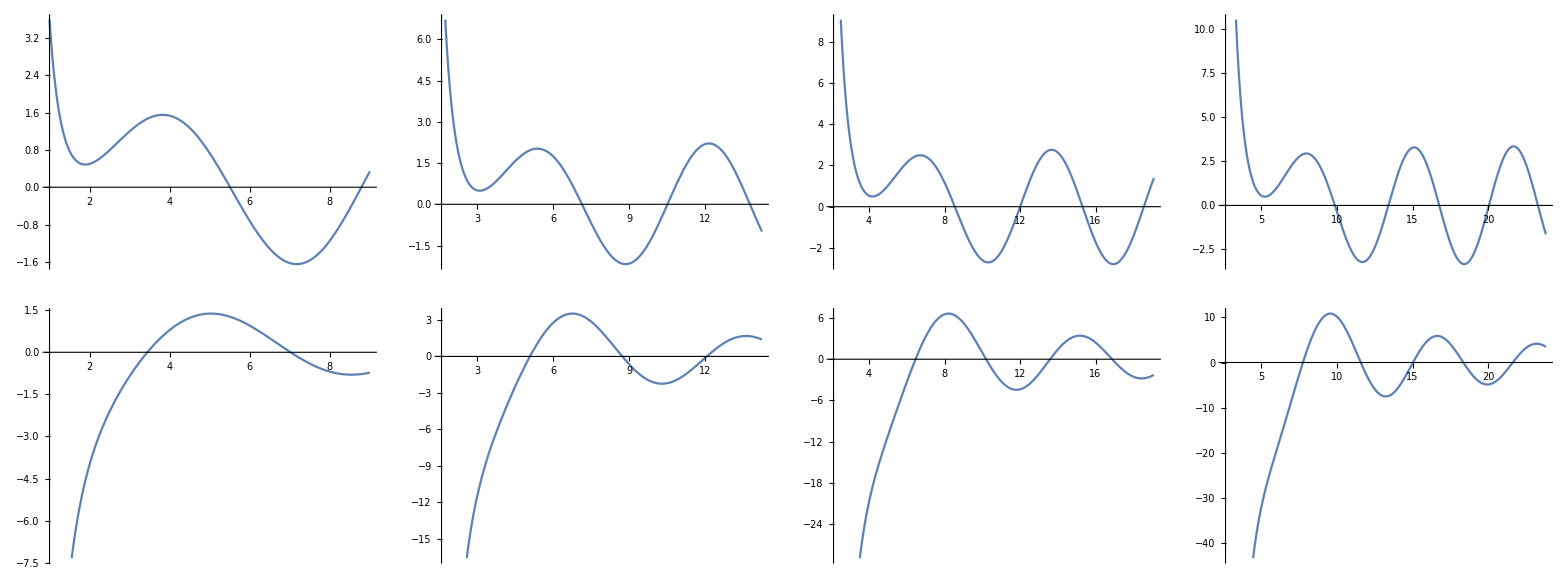

```mathematica
Grid[{
Table[plt[sln[Generic][2,3][l]],{l,2,5}],
Table[plt[sln[Generic][1,3][l]],{l,2,5}]
},Frame->All]
```

### Волны в дальней зоне

#### Нечетные моды (радиальные части)

```mathematica
sln[Far][2,3][l_]:=sde[Far][2,3][l];
sln[Far][1,3][l_][r_]:=0;
```

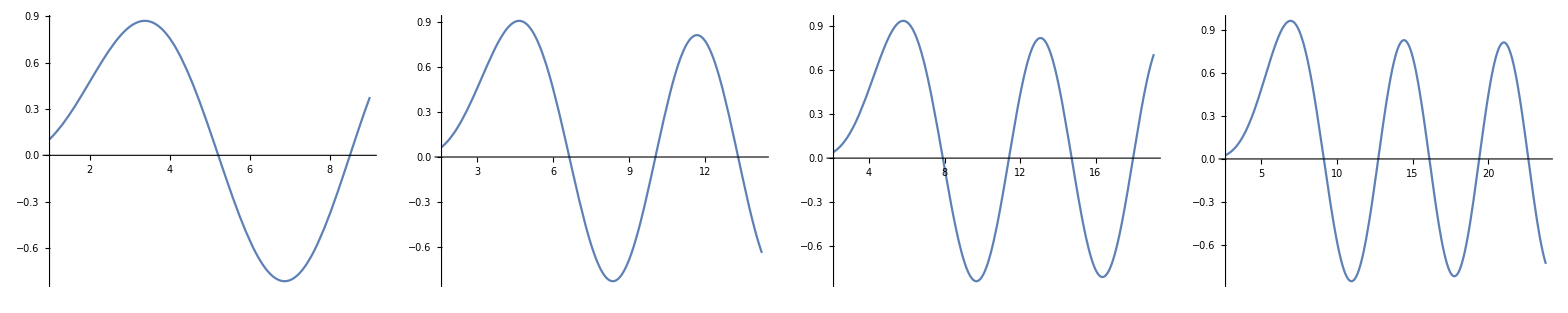

```mathematica
Grid[{
Table[plt[sln[Far][2,3][l]],{l,2,5}]
},Frame->All]
```

#### Нечетные моды (базовые, общий вид)

```mathematica
sln[Far][Odd][l0_][r_,u_]:=(tha[l0][r,u]//thmasked[Odd])/.{f[1,3][l0]:>(0&),f[2,3][l0]:>(Decay@sln[Far][2,3][l0][#]&)};
```

#### [В процессе] Интерференция двух равнопараметрических нечетных мод

```mathematica
sln[Far][Odd][l][r-r0,u][{2,3}];
sln[Far][Odd][l][r,u][{2,3}];
Grid[{{Manipulate[DensityPlot[%+%%/.{l->2},{r,0,50},{u,0,π}],{r0,-50,0},{l,2,10,1}],
Manipulate[DensityPlot[%+%%/.{l->2},{r,1000,1050},{u,0,π},MaxRecursion->3],{r0,1000-50,1000},{l,2,10,1}]}}]
```

|

#### [В процессе] Плотность энергии нечетных мод с разными L

```mathematica
series[Far][Odd][{n_Integer}]:=Module[{l},Table[series[Far][Odd][l],{l,2,n}]];
series[Far][Odd][l0_Integer]:=Module[{l,m,s,sl},
s=Parameterize[sln[Far][Odd][l][r,u],l->l0, "m"->0];
sl={s//Decay};
Do[AppendTo[sl,(s=up[All][s][u,w])//Decay],{m,1,l0}];
sl
];
```

```mathematica
cache[series]=series[Far][Odd][{4}];
cache[series,Tensor]=Table[j Exp[-I t]//MakeTensor[#][r,u]&,{i,cache[series]},{j,i}];
```

```mathematica
cache[series,energy]=Table[EvaluateAt[epsne,{th[a_,b_]:>j[[a,b]]}],{i,cache[series,Tensor]},{j,i}]//Simplify;
```

```mathematica
Plot3D[Log[#],{r,0.1,50},{u,0,π},MaxRecursion->5,PlotRange->Full,AxesLabel->Automatic,PlotLegends->"Expressions"]&/@({cache[series,energy][[1,1]],cache[series,energy][[2,3]],cache[series,energy][[-1,-1]]}/.{t->0,w->0})
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}